### Setup

```mathematica
NULLEFFECTSDataNM=Import["/Users/janhannig/Dropbox/Documents/Research/Shevaun/Null Effects paper/Mathematica_code/NULLEFFECTSDATA_missingDeleted.csv","IgnoreEmptyLines" -> True,"HeaderLines" -> 2];(*Enter path to the data file*)
```

```mathematica
idStressor=9;(*health*)
```

```mathematica
n=Length[NULLEFFECTSDataNM⟦All,8⟧]
```

1438

```mathematica
Age=Map[Function[x,If[x>40,1,0]],NULLEFFECTSDataNM⟦All,2⟧];
```

```mathematica
IDlist=Union[NULLEFFECTSDataNM⟦All,1⟧];
```

```mathematica
m=Length[IDlist]
```

219

```mathematica
IDindicator=Flatten@Map[Function[x,Position[IDlist,x]], NULLEFFECTSDataNM⟦All,1⟧];
```

```mathematica
iW=Table[Subscript[w, i],{i,1,m}];
```

```mathematica
vW=Map[Function[x,Subscript[w, x]],IDindicator];
```

```mathematica
WellBeing=Floor[10NULLEFFECTSDataNM⟦All,3⟧]/10;(*NULLEFFECTSDataNM⟦All,3⟧;*)
```

```mathematica
Stress=NULLEFFECTSDataNM⟦All,idStressor⟧;
```

```mathematica
s=Plus@@Stress
```

64

```mathematica
a=Apply[Plus,Stress Age]
```

23

```mathematica
StressxIDlist=Union[NULLEFFECTSDataNM⟦All,{1,idStressor}⟧];
```

```mathematica
l=Length[StressxIDlist]
```

258

```mathematica
StressxIDindicator=Flatten@Map[Function[x,Position[StressxIDlist,x]], NULLEFFECTSDataNM⟦All,{1,idStressor}⟧];
```

```mathematica
iU=Table[Subscript[u, i],{i,1,l}];
```

```mathematica
vU=Map[Function[x,Subscript[u, x]],StressxIDindicator];
```

```mathematica
MyPrecision=10^10;
```

```mathematica
g1range={g1,.03,.3};g2range={g2,0,.5};g3range={g3,0,.5};g4range={g4,0.1,2};
```

## AGE, Random Intercept

### Model 0

```mathematica
cLOGlikelihood0=Expand[-1/2 Apply[Plus,(WellBeing-b0 -b1 Age -vW)^2]-(n g1)/(2m)Apply[Plus,iW^2]];
```

```mathematica
parameters0=Join[{b0,b1},iW];zeros0=Join[{b0->0,b1->0},Table[Subscript[w, i]->0,{i,1,m}]];
```

```mathematica
Hessian0=Simplify@Table[-D[cLOGlikelihood0,parameters0⟦i⟧,parameters0⟦j⟧],{i,1,2+m},{j,1,2+m}];
```

```mathematica
gradient0=Simplify@Table[-D[cLOGlikelihood0,parameters0⟦i⟧],{i,1,2+m}]/.zeros0;
```

```mathematica
detH0[g1_]=Simplify@Det[Hessian0];
```

```mathematica
LOGdetH0[g1_]=PowerExpand@Log@detH0[g1];
```

```mathematica
mean0=-LinearSolve[Hessian0,gradient0];
```

```mathematica
exponent0[g1_]=Expand[-1/2 Apply[Plus,WellBeing^2]]-Expand[1/2 Apply[Plus,mean0 gradient0]];
```

```mathematica
(*LOGpIposterior0[g1_]=PowerExpand@Log[(((n g1)/m)^(m/2)Gamma[(n-2)/2])/((2π)^((n-2)/2)detH0[g1]^(1/2)(-exponent0[g1])^((n-2)/2))Exp[-g1/2]/(√(2 π g1))];*)
```

```mathematica
LOGpIposterior0[g1_]=m/2 Log[(n g1)/m]+LogGamma[(n-2)/2]-(n-2)/2 Log[-exponent0[g1]]-(n-1)/2 Log[2π]-1/2 Log[g1]-1/2 LOGdetH0[g1]-g1/2;
```

Laplace Approximation

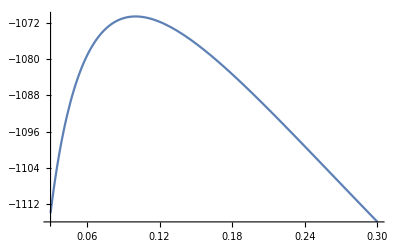

```mathematica
Plot[LOGpIposterior0[g1],g1range]
```

```mathematica
max0=NMaximize[{LOGpIposterior0[g1],g1range⟦2⟧<g1<g1range⟦3⟧},g1]
```

{-1070.64,{g1→0.100195}}

```mathematica
g10=Round[max0⟦2,1,2⟧ MyPrecision]/MyPrecision;
```

```mathematica
laH0=-D[LOGpIposterior0[g1],{g1,2}]/.{g1->g10};
```

```mathematica
LOGpIposterior0[g10]//N
```

-1070.64

```mathematica
laLOGm0=LOGpIposterior0[g10]+1/2 Log[2π]-1/2 Log[laH0]//N
```

-1074.15

```mathematica
pointEstimator0=mean0/.{g1->g10}//N;
pointEstimator0⟦1⟧ (*intercept*)
pointEstimator0⟦2⟧ (*slope Age*)
Variance[pointEstimator0⟦Range[3,m+2]⟧] (*variance of random intercept*)
(-2exponent0[max0⟦2,1,2⟧])/(n-2)(* variance of residual*)
```

1.82141

-0.450336

0.239659

0.181827

## AGE, Random Intercept + STRESS

### Model 1a

```mathematica
g20=1/MyPrecision;(* g20 is at 0 from repeats, updating g1 *)
```

```mathematica
cLOGlikelihood1=Expand[-1/2 Apply[Plus,(WellBeing-b0 -b1 Age -b2 Stress-vW)^2]-(n g1)/(2m)Apply[Plus,iW^2]-(s g2)/2 b2^2]/.g2->g20;
```

```mathematica
parameters1=Join[{b0,b1,b2},iW];zeros1=Join[{b0->0,b1->0,b2->0},Table[Subscript[w, i]->0,{i,1,m}]];
```

```mathematica
Hessian1=Simplify@Table[-D[cLOGlikelihood1,parameters1⟦i⟧,parameters1⟦j⟧],{i,1,3+m},{j,1,3+m}];
```

```mathematica
gradient1=Simplify@Table[-D[cLOGlikelihood1,parameters1⟦i⟧],{i,1,3+m}]/.zeros1;
```

```mathematica
detH1[g1_,g2_]=Simplify@Det[Hessian1];
```

```mathematica
LOGdetH1[g1_,g2_]=PowerExpand@Log@detH1[g1,g2];
```

```mathematica
mean1=-LinearSolve[Hessian1,gradient1];
```

```mathematica
exponent1[g1_,g2_]=Expand[-1/2 Apply[Plus,WellBeing^2]]-Expand[1/2 Apply[Plus,mean1  gradient1]];
```

```mathematica
(*LOGpIposterior1[g1_,g2_]=PowerExpand@Log[(((n g1)/m)^(m/2)(s g2)^(1/2)Gamma[(n-2)/2])/((2π)^((n-2)/2)detH1[g1,g2]^(1/2)(-exponent1[g1,g2])^((n-2)/2))Exp[-g1/2]/(√(2 π g1))Exp[-g2/2]/(√(2 π g2))];*)
```

```mathematica
LOGpIposterior1[g1_,g2_]=m/2 Log[(n g1)/m]+1/2 Log[s g2]+LogGamma[(n-2)/2]-(n-2)/2 Log[-exponent1[g1,g2]]-n/2 Log[2π]-1/2 Log[g1 g2]-1/2 LOGdetH1[g1,g2]-g1/2-g2/2;
```

### Laplace Approximation

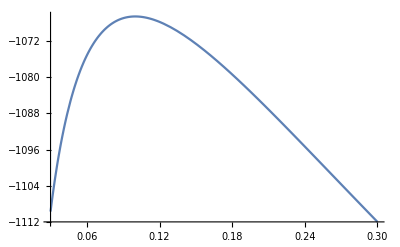

```mathematica
Plot[LOGpIposterior1[g1,g20],g1range]
```

```mathematica
max1=NMaximize[{LOGpIposterior1[g1,g20],g1range⟦2⟧<g1<g1range⟦3⟧},g1]
```

{-1066.52,{g1→0.0999486}}

```mathematica
g10=Round[max1⟦2,1,2⟧ MyPrecision]/MyPrecision;
```

```mathematica
laH1g1=-D[LOGpIposterior1[g1,g20],{g1,2}]/.{g1->g10};
```

```mathematica
(*normal approximation in g1 exponential approximation in g2*)
```

```mathematica
LOGpIposterior1[g10,g20]//N
```

-1066.52

### Model 1b

```mathematica
(*updating g2, g1 from 1a*)
```

```mathematica
cLOGlikelihood1=Expand[-1/2 Apply[Plus,(WellBeing-b0 -b1 Age -b2 Stress-vW)^2]-(n g1)/(2m)Apply[Plus,iW^2]-(s g2)/2 b2^2]/.g1->g10;
```

```mathematica
parameters1=Join[{b0,b1,b2},iW];zeros1=Join[{b0->0,b1->0,b2->0},Table[Subscript[w, i]->0,{i,1,m}]];
```

```mathematica
Hessian1=Simplify@Table[-D[cLOGlikelihood1,parameters1⟦i⟧,parameters1⟦j⟧],{i,1,3+m},{j,1,3+m}];
```

```mathematica
gradient1=Simplify@Table[-D[cLOGlikelihood1,parameters1⟦i⟧],{i,1,3+m}]/.zeros1;
```

```mathematica
detH1[g1_,g2_]=Simplify@Det[Hessian1];
```

```mathematica
LOGdetH1[g1_,g2_]=PowerExpand@Log@detH1[g1,g2];
```

```mathematica
mean1=-LinearSolve[Hessian1,gradient1];
```

```mathematica
exponent1[g1_,g2_]=Expand[-1/2 Apply[Plus,WellBeing^2]]-Expand[1/2 Apply[Plus,mean1  gradient1]];
```

```mathematica
(*LOGpIposterior1[g1_,g2_]=PowerExpand@Log[(((n g1)/m)^(m/2)(s g2)^(1/2)Gamma[(n-2)/2])/((2π)^((n-2)/2)detH1[g1,g2]^(1/2)(-exponent1[g1,g2])^((n-2)/2))Exp[-g1/2]/(√(2 π g1))Exp[-g2/2]/(√(2 π g2))];*)
```

```mathematica
LOGpIposterior1[g1_,g2_]=m/2 Log[(n g1)/m]+1/2 Log[s g2]+LogGamma[(n-2)/2]-(n-2)/2 Log[-exponent1[g1,g2]]-n/2 Log[2π]-1/2 Log[g1 g2]-1/2 LOGdetH1[g1,g2]-g1/2-g2/2;
```

### Laplace Approximation

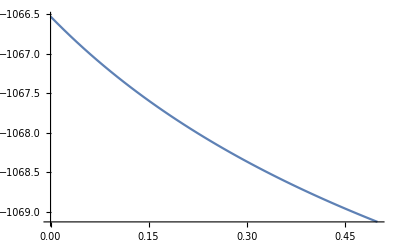

```mathematica
Plot[LOGpIposterior1[g10,g2],g2range]
```

```mathematica
g20=1/MyPrecision;(*nearly 0 - need an exponential approximation*)
```

```mathematica
laH1g2=-D[LOGpIposterior1[g10,g2],{g2,1}]/.{g2->g20};
```

```mathematica
LOGpIposterior1[g10,g20]//N
```

-1066.52

#### Final Accounting

```mathematica
laLOGm1=LOGpIposterior1[g10,g20]+1/2 Log[2π]-1/2 Log[laH1g1]-Log[laH1g2]//N
```

-1072.18

```mathematica
B10=Exp[laLOGm1-laLOGm0]//N
```

7.17996

```mathematica
lB10=(laLOGm1-laLOGm0)/Log[10.]
```

0.856122

```mathematica
pointEstimator1=mean1/.{g1->g10,g2->g20}//N;
pointEstimator1⟦1⟧ (*intercept*)
pointEstimator1⟦3⟧ (*slope Stress*)
pointEstimator1⟦2⟧ (*slope Age*)
Variance[pointEstimator1⟦Range[4,m+3]⟧] (*variance of random intercept*)
(-2.exponent1[max1⟦2,1,2⟧,g20])/(n-2)(* variance of residual*)
```

1.80944

0.202523

-0.444309

0.238578

0.180548

## AGE, Random Intercept, STRESS + STRESSxAGE

### Model 2a

```mathematica
g30=1/MyPrecision;(*g3, g2 near 0 from iteration, computing g3*)
```

```mathematica
(*updating g1*)
```

```mathematica
cLOGlikelihood2=Expand[-1/2 Apply[Plus,(WellBeing-b0 -b1 Age -b2 Stress-b3 Age Stress - vW)^2]-(n g1)/(2m)Apply[Plus,iW^2]-(s g2)/2 b2^2-(a g3)/2 b3^2]/.{g2->g20,g3->g30};
```

```mathematica
parameters2=Join[{b0,b1,b2,b3},iW];zeros2=Join[{b0->0,b1->0,b2->0,b3->0},Table[Subscript[w, i]->0,{i,1,m}]];
```

```mathematica
Hessian2=Simplify@Table[-D[cLOGlikelihood2,parameters2⟦i⟧,parameters2⟦j⟧],{i,1,4+m},{j,1,4+m}];
```

```mathematica
gradient2=Simplify@Table[-D[cLOGlikelihood2,parameters2⟦i⟧],{i,1,4+m}]/.zeros2;
```

```mathematica
detH2[g1_,g2_,g3_]=Simplify@Det[Hessian2];
```

```mathematica
LOGdetH2[g1_,g2_,g3_]=PowerExpand@Log@detH2[g1,g2,g3];
```

```mathematica
mean2=-LinearSolve[Hessian2,gradient2];
```

```mathematica
exponent2[g1_,g2_,g3_]=Expand[-1/2 Apply[Plus,WellBeing^2]]-Expand[1/2 Apply[Plus,mean2 gradient2]];
```

```mathematica
(*LOGpIposterior1[g1_,g2_]=PowerExpand@Log[(((n g1)/m)^(m/2)(s g2)^(1/2)(a g3)^(1/2)Gamma[(n-2)/2])/((2π)^((n-2)/2)detH2[g1,g2,g3]^(1/2)(-exponent2[g1,g2,g3])^((n-2)/2))Exp[-g1/2]/(√(2 π g1))Exp[-g2/2]/(√(2 π g2))Exp[-g3/2]/(√(2 π g3))];*)
```

```mathematica
LOGpIposterior2[g1_,g2_,g3_]=m/2 Log[(n g1)/m]+1/2 Log[s g2]+1/2 Log[a g3]+LogGamma[(n-2)/2]-(n-2)/2 Log[-exponent2[g1,g2,g3]]-(n+1)/2 Log[2π]-1/2 Log[g1 g2 g3]-1/2 LOGdetH2[g1,g2,g3]-g1/2-g2/2-g3/2;
```

### Laplace Approximation

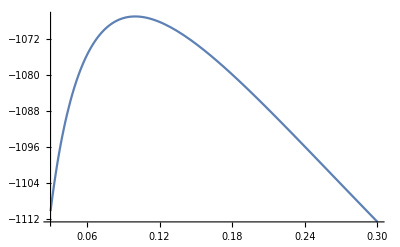

```mathematica
Plot[LOGpIposterior2[g1,g20,g30],g1range]
```

```mathematica
max2=NMaximize[{LOGpIposterior2[g1,g20,g30],g1range⟦2⟧<g1<g1range⟦3⟧},g1](*very small change*)
```

{-1067.01,{g1→0.0998787}}

```mathematica
g10=Round[max2⟦2,1,2⟧ MyPrecision]/MyPrecision ;
```

```mathematica
laH2g1=-D[LOGpIposterior2[g1,g20,g30],{g1,2}]/.{g1->g10};
```

```mathematica
(*normal approximation in g1 exponential approximation in g2 and g3*)
```

```mathematica
LOGpIposterior2[g10,g20,g30]//N
```

-1067.01

### Model 2b

```mathematica
(*updating g3*)
```

```mathematica
cLOGlikelihood2=Expand[-1/2 Apply[Plus,(WellBeing-b0 -b1 Age -b2 Stress-b3 Age Stress - vW)^2]-(n g1)/(2m)Apply[Plus,iW^2]-(s g2)/2 b2^2-(a g3)/2 b3^2]/.{g1->g10,g2->g20};
```

```mathematica
parameters2=Join[{b0,b1,b2,b3},iW];zeros2=Join[{b0->0,b1->0,b2->0,b3->0},Table[Subscript[w, i]->0,{i,1,m}]];
```

```mathematica
Hessian2=Simplify@Table[-D[cLOGlikelihood2,parameters2⟦i⟧,parameters2⟦j⟧],{i,1,4+m},{j,1,4+m}];
```

```mathematica
gradient2=Simplify@Table[-D[cLOGlikelihood2,parameters2⟦i⟧],{i,1,4+m}]/.zeros2;
```

```mathematica
detH2[g1_,g2_,g3_]=Simplify@Det[Hessian2];
```

```mathematica
LOGdetH2[g1_,g2_,g3_]=PowerExpand@Log@detH2[g1,g2,g3];
```

```mathematica
mean2=-LinearSolve[Hessian2,gradient2];
```

```mathematica
exponent2[g1_,g2_,g3_]=Expand[-1/2 Apply[Plus,WellBeing^2]]-Expand[1/2 Apply[Plus,mean2 gradient2]];
```

```mathematica
(*LOGpIposterior1[g1_,g2_]=PowerExpand@Log[(((n g1)/m)^(m/2)(s g2)^(1/2)(a g3)^(1/2)Gamma[(n-2)/2])/((2π)^((n-2)/2)detH2[g1,g2,g3]^(1/2)(-exponent2[g1,g2,g3])^((n-2)/2))Exp[-g1/2]/(√(2 π g1))Exp[-g2/2]/(√(2 π g2))Exp[-g3/2]/(√(2 π g3))];*)
```

```mathematica
LOGpIposterior2[g1_,g2_,g3_]=m/2 Log[(n g1)/m]+1/2 Log[s g2]+1/2 Log[a g3]+LogGamma[(n-2)/2]-(n-2)/2 Log[-exponent2[g1,g2,g3]]-(n+1)/2 Log[2π]-1/2 Log[g1 g2 g3]-1/2 LOGdetH2[g1,g2,g3]-g1/2-g2/2-g3/2;
```

### Laplace Approximation

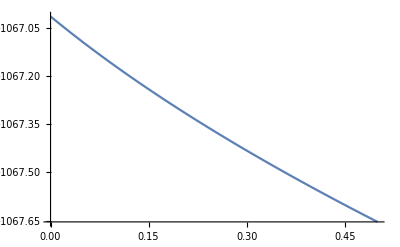

```mathematica
Plot[LOGpIposterior2[g10,g20,g3],g3range]
```

```mathematica
(*nearly 0 - need an exponential approximation*)
```

```mathematica
laH2g3=-D[LOGpIposterior2[g10,g20,g3],{g3,1}]/.{g3->g30};
```

```mathematica
LOGpIposterior2[g10,g20,g30]//N
```

-1067.01

### Model 2c

```mathematica
(*updating g2*)
```

```mathematica
cLOGlikelihood2=Expand[-1/2 Apply[Plus,(WellBeing-b0 -b1 Age -b2 Stress-b3 Age Stress - vW)^2]-(n g1)/(2m)Apply[Plus,iW^2]-(s g2)/2 b2^2-(a g3)/2 b3^2]/.{g1->g10,g3->g30};
```

```mathematica
parameters2=Join[{b0,b1,b2,b3},iW];zeros2=Join[{b0->0,b1->0,b2->0,b3->0},Table[Subscript[w, i]->0,{i,1,m}]];
```

```mathematica
Hessian2=Simplify@Table[-D[cLOGlikelihood2,parameters2⟦i⟧,parameters2⟦j⟧],{i,1,4+m},{j,1,4+m}];
```

```mathematica
gradient2=Simplify@Table[-D[cLOGlikelihood2,parameters2⟦i⟧],{i,1,4+m}]/.zeros2;
```

```mathematica
detH2[g1_,g2_,g3_]=Simplify@Det[Hessian2];
```

```mathematica
LOGdetH2[g1_,g2_,g3_]=PowerExpand@Log@detH2[g1,g2,g3];
```

```mathematica
mean2=-LinearSolve[Hessian2,gradient2];
```

```mathematica
exponent2[g1_,g2_,g3_]=Expand[-1/2 Apply[Plus,WellBeing^2]]-Expand[1/2 Apply[Plus,mean2 gradient2]];
```

```mathematica
(*LOGpIposterior1[g1_,g2_]=PowerExpand@Log[(((n g1)/m)^(m/2)(s g2)^(1/2)(a g3)^(1/2)Gamma[(n-2)/2])/((2π)^((n-2)/2)detH2[g1,g2,g3]^(1/2)(-exponent2[g1,g2,g3])^((n-2)/2))Exp[-g1/2]/(√(2 π g1))Exp[-g2/2]/(√(2 π g2))Exp[-g3/2]/(√(2 π g3))];*)
```

```mathematica
LOGpIposterior2[g1_,g2_,g3_]=m/2 Log[(n g1)/m]+1/2 Log[s g2]+1/2 Log[a g3]+LogGamma[(n-2)/2]-(n-2)/2 Log[-exponent2[g1,g2,g3]]-(n+1)/2 Log[2π]-1/2 Log[g1 g2 g3]-1/2 LOGdetH2[g1,g2,g3]-g1/2-g2/2-g3/2;
```

### Laplace Approximation

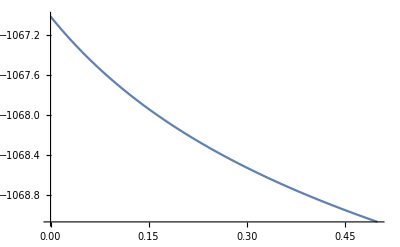

```mathematica
Plot[LOGpIposterior2[g10,g2,g30],g2range]
```

```mathematica
(*nearly 0 - need an exponential approximation, no change to g20 *)
```

```mathematica
laH2g2=-D[LOGpIposterior2[g10,g2,g30],{g2,1}]/.{g2->g20};
```

```mathematica
LOGpIposterior2[g10,g20,g30]//N
```

-1067.01

#### Final Accounting

```mathematica
laLOGm2=LOGpIposterior2[g10,g20,g30]+1/2 Log[2π]-1/2 Log[laH2g1]-Log[laH2g2]-Log[laH2g2]//N
```

-1074.72

```mathematica
B21=Exp[laLOGm2-laLOGm1]//N
```

0.0788289

```mathematica
lB21=(laLOGm2-laLOGm1)/Log[10.]
```

-1.10331

```mathematica
pointEstimator2=mean2/.{g1->g10,g2->g20, g3-> g30}//N;
pointEstimator2⟦1⟧ (*intercept*)
pointEstimator2⟦3⟧ (*slope Stress*)
pointEstimator2⟦2⟧ (*slope Age*)
Variance[pointEstimator2⟦Range[5,m+4]⟧] (*variance of random intercept*)
(-2.exponent2[max2⟦2,1,2⟧,g20,g30])/(n-2)(* variance of residual*)
```

1.81021

0.189452

-0.445629

0.238688

0.180525

## AGE, Random Intercept, STRESS + Random Slope

### Model 3aS1

```mathematica
(*g10 from previous models, g20  near 0, computing g4*)g10//N
```

0.0998787

```mathematica
cLOGlikelihood3=Expand[-1/2 Apply[Plus,(WellBeing-b0 -b1 Age -b2 Stress-vW-vU)^2]-(n g1)/(2m)Apply[Plus,iW^2]-(s g2)/2 b2^2-(n g4)/(2l)Apply[Plus,iU^2]]/.{g1->g10,g2->g20};
```

```mathematica
parameters3=Join[{b0,b1,b2},iW,iU];zeros3=Join[{b0->0,b1->0,b2->0},Table[Subscript[w, i]->0,{i,1,m}],Table[Subscript[u, i]->0,{i,1,l}]];
```

```mathematica
Hessian3=Simplify@Table[-D[cLOGlikelihood3,parameters3⟦i⟧,parameters3⟦j⟧],{i,1,3+m+l},{j,1,3+m+l}];
```

```mathematica
gradient3=Simplify@Table[-D[cLOGlikelihood3,parameters3⟦i⟧],{i,1,3+m+l}]/.zeros3;
```

```mathematica
detH3[g1_,g2_,g4_]=Simplify@Det[Hessian3];
```

```mathematica
LOGdetH3[g1_,g2_,g4_]=PowerExpand@Log@detH3[g1,g2,g4];
```

```mathematica
mean3=-LinearSolve[Hessian3,gradient3];
```

```mathematica
exponent3[g1_,g2_,g4_]=Expand[-1/2 Apply[Plus,WellBeing^2]]-1/2 Apply[Plus,mean3 gradient3];
```

```mathematica
(*.10 LOGpI2[g1_,g2_,g4_]=PowerExpand@Log[(((n g1)/m)^(m/2)(s g2)^(1/2)((n g4)/l)^(l/2)Gamma[(n-2)/2])/((2π)^((n-2)/2)detH3[g1,g2,g4]^(1/2)(-exponent3[g1,g2,g4])^((n-2)/2))Exp[-g1/2]/(√(2 π g1))Exp[-g2/2]/(√(2 π g2))Exp[-g4/2]/(√(2 π g4))];*)
```

```mathematica
LOGpIposterior3[g1_,g2_,g4_]=m/2 Log[(n g1)/m]+l/2 Log[(n g4)/l]+1/2 Log[s g2]+LogGamma[(n-2)/2]-(n-2)/2 Log[-exponent3[g1,g2,g4]]-(n+1)/2 Log[2π]-1/2 Log[g1 g2 g4]-1/2 LOGdetH3[g1,g2,g4]-g1/2-g2/2-g4/2;
```

### Laplace Approximation

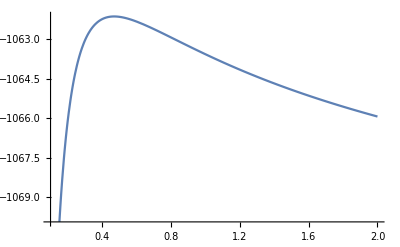

```mathematica
Plot[LOGpIposterior3[g10,g20,g4],g4range]
```

```mathematica
max3a=NMaximize[{LOGpIposterior3[g10,g20,g4],g4range⟦2⟧<g4<g4range⟦3⟧},g4]
```

{-1062.15,{g4→0.469592}}

```mathematica
g40=Round[max3a⟦2,1,2⟧ MyPrecision]/MyPrecision;
```

```mathematica
LOGpIposterior3[g10,g20,g40]//N
```

-1062.15

### Model 3bS1

```mathematica
(*updating g1*)g40//N
```

0.469592

```mathematica
cLOGlikelihood3=Expand[-1/2 Apply[Plus,(WellBeing-b0 -b1 Age -b2 Stress-vW-vU)^2]-(n g1)/(2m)Apply[Plus,iW^2]-(s g2)/2 b2^2-(n g4)/(2l)Apply[Plus,iU^2]]/.{g2->g20,g4->g40};
```

```mathematica
Hessian3=Simplify@Table[-D[cLOGlikelihood3,parameters3⟦i⟧,parameters3⟦j⟧],{i,1,3+m+l},{j,1,3+m+l}];
```

```mathematica
gradient3=Simplify@Table[-D[cLOGlikelihood3,parameters3⟦i⟧],{i,1,3+m+l}]/.zeros3;
```

```mathematica
detH3[g1_,g2_,g4_]=Simplify@Det[Hessian3];
```

```mathematica
LOGdetH3[g1_,g2_,g4_]=PowerExpand@Log@detH3[g1,g2,g4];
```

```mathematica
mean3=-LinearSolve[Hessian3,gradient3];
```

```mathematica
exponent3[g1_,g2_,g4_]=Expand[-1/2 Apply[Plus,WellBeing^2]]-1/2 Apply[Plus,mean3 gradient3];
```

```mathematica
(*.10 LOGpI2[g1_,g2_,g4_]=PowerExpand@Log[(((n g1)/m)^(m/2)(s g2)^(1/2)((n g4)/l)^(l/2)Gamma[(n-2)/2])/((2π)^((n-2)/2)detH3[g1,g2,g4]^(1/2)(-exponent3[g1,g2,g4])^((n-2)/2))Exp[-g1/2]/(√(2 π g1))Exp[-g2/2]/(√(2 π g2))Exp[-g4/2]/(√(2 π g4))];*)
```

```mathematica
LOGpIposterior3[g1_,g2_,g4_]=m/2 Log[(n g1)/m]+l/2 Log[(n g4)/l]+1/2 Log[s g2]+LogGamma[(n-2)/2]-(n-2)/2 Log[-exponent3[g1,g2,g4]]-(n+1)/2 Log[2π]-1/2 Log[g1 g2 g4]-1/2 LOGdetH3[g1,g2,g4]-g1/2-g2/2-g4/2;
```

### Laplace Approximation

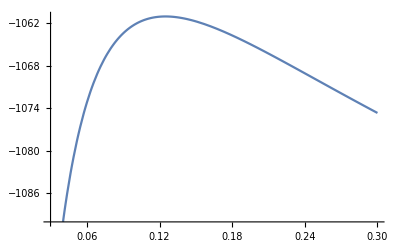

```mathematica
Plot[LOGpIposterior3[g1,g20,g40],g1range]
```

```mathematica
max3b=NMaximize[{LOGpIposterior3[g1,g20,g40],g1range⟦2⟧<g1<g1range⟦3⟧},g1](*very small change*)
```

{-1061.06,{g1→0.124938}}

```mathematica
g10=Round[max3b⟦2,1,2⟧ MyPrecision]/MyPrecision ;
```

```mathematica
LOGpIposterior3[g10,g20,g40]//N
```

-1061.06

### Model 3aS2

```mathematica
(*g40 from previous iteration, g20, g30 near 0, computing g4*)g10//N
```

0.124938

```mathematica
cLOGlikelihood3=Expand[-1/2 Apply[Plus,(WellBeing-b0 -b1 Age -b2 Stress-vW-vU)^2]-(n g1)/(2m)Apply[Plus,iW^2]-(s g2)/2 b2^2-(n g4)/(2l)Apply[Plus,iU^2]]/.{g1->g10,g2->g20};
```

```mathematica
parameters3=Join[{b0,b1,b2},iW,iU];zeros3=Join[{b0->0,b1->0,b2->0},Table[Subscript[w, i]->0,{i,1,m}],Table[Subscript[u, i]->0,{i,1,l}]];
```

```mathematica
Hessian3=Simplify@Table[-D[cLOGlikelihood3,parameters3⟦i⟧,parameters3⟦j⟧],{i,1,3+m+l},{j,1,3+m+l}];
```

```mathematica
gradient3=Simplify@Table[-D[cLOGlikelihood3,parameters3⟦i⟧],{i,1,3+m+l}]/.zeros3;
```

```mathematica
detH3[g1_,g2_,g4_]=Simplify@Det[Hessian3];
```

```mathematica
LOGdetH3[g1_,g2_,g4_]=PowerExpand@Log@detH3[g1,g2,g4];
```

```mathematica
mean3=-LinearSolve[Hessian3,gradient3];
```

```mathematica
exponent3[g1_,g2_,g4_]=Expand[-1/2 Apply[Plus,WellBeing^2]]-1/2 Apply[Plus,mean3 gradient3];
```

```mathematica
(*.10 LOGpI2[g1_,g2_,g4_]=PowerExpand@Log[(((n g1)/m)^(m/2)(s g2)^(1/2)((n g4)/l)^(l/2)Gamma[(n-2)/2])/((2π)^((n-2)/2)detH3[g1,g2,g4]^(1/2)(-exponent3[g1,g2,g4])^((n-2)/2))Exp[-g1/2]/(√(2 π g1))Exp[-g2/2]/(√(2 π g2))Exp[-g4/2]/(√(2 π g4))];*)
```

```mathematica
LOGpIposterior3[g1_,g2_,g4_]=m/2 Log[(n g1)/m]+l/2 Log[(n g4)/l]+1/2 Log[s g2]+LogGamma[(n-2)/2]-(n-2)/2 Log[-exponent3[g1,g2,g4]]-(n+1)/2 Log[2π]-1/2 Log[g1 g2 g4]-1/2 LOGdetH3[g1,g2,g4]-g1/2-g2/2-g4/2;
```

### Laplace Approximation

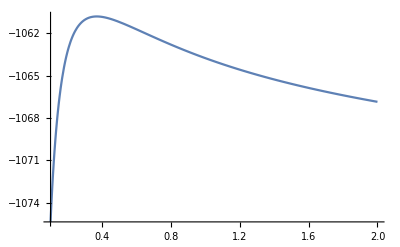

```mathematica
Plot[LOGpIposterior3[g10,g20,g4],g4range]
```

```mathematica
max3a=NMaximize[{LOGpIposterior3[g10,g20,g4],g4range⟦2⟧<g4<g4range⟦3⟧},g4]
```

{-1060.8,{g4→0.368428}}

```mathematica
g40=Round[max3a⟦2,1,2⟧ MyPrecision]/MyPrecision;
```

```mathematica
laH3g4=-D[LOGpIposterior3[g10,g20,g4],{g4,2}]/.g4->g40;
```

```mathematica
LOGpIposterior3[g10,g20,g40]//N
```

-1060.8

### Model 3bS2

```mathematica
(*updating g1*)g40//N
```

0.368428

```mathematica
cLOGlikelihood3=Expand[-1/2 Apply[Plus,(WellBeing-b0 -b1 Age -b2 Stress-vW-vU)^2]-(n g1)/(2m)Apply[Plus,iW^2]-(s g2)/2 b2^2-(n g4)/(2l)Apply[Plus,iU^2]]/.{g2->g20,g4->g40};
```

```mathematica
Hessian3=Simplify@Table[-D[cLOGlikelihood3,parameters3⟦i⟧,parameters3⟦j⟧],{i,1,3+m+l},{j,1,3+m+l}];
```

```mathematica
gradient3=Simplify@Table[-D[cLOGlikelihood3,parameters3⟦i⟧],{i,1,3+m+l}]/.zeros3;
```

```mathematica
detH3[g1_,g2_,g4_]=Simplify@Det[Hessian3];
```

```mathematica
LOGdetH3[g1_,g2_,g4_]=PowerExpand@Log@detH3[g1,g2,g4];
```

```mathematica
mean3=-LinearSolve[Hessian3,gradient3];
```

```mathematica
exponent3[g1_,g2_,g4_]=Expand[-1/2 Apply[Plus,WellBeing^2]]-1/2 Apply[Plus,mean3 gradient3];
```

```mathematica
(*.10 LOGpI2[g1_,g2_,g4_]=PowerExpand@Log[(((n g1)/m)^(m/2)(s g2)^(1/2)((n g4)/l)^(l/2)Gamma[(n-2)/2])/((2π)^((n-2)/2)detH3[g1,g2,g4]^(1/2)(-exponent3[g1,g2,g4])^((n-2)/2))Exp[-g1/2]/(√(2 π g1))Exp[-g2/2]/(√(2 π g2))Exp[-g4/2]/(√(2 π g4))];*)
```

```mathematica
LOGpIposterior3[g1_,g2_,g4_]=m/2 Log[(n g1)/m]+l/2 Log[(n g4)/l]+1/2 Log[s g2]+LogGamma[(n-2)/2]-(n-2)/2 Log[-exponent3[g1,g2,g4]]-(n+1)/2 Log[2π]-1/2 Log[g1 g2 g4]-1/2 LOGdetH3[g1,g2,g4]-g1/2-g2/2-g4/2;
```

### Laplace Approximation

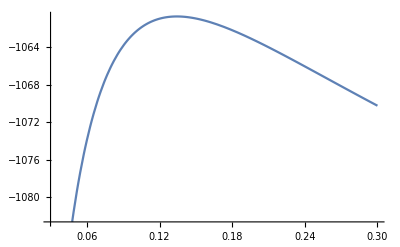

```mathematica
Plot[LOGpIposterior3[g1,g20,g40],g1range]
```

```mathematica
max3b=NMaximize[{LOGpIposterior3[g1,g20,g40],g1range⟦2⟧<g1<g1range⟦3⟧},g1](*very small change*)
```

{-1060.7,{g1→0.134362}}

```mathematica
g10=Round[max3b⟦2,1,2⟧ MyPrecision]/MyPrecision ;
```

```mathematica
laH3g1=-D[LOGpIposterior3[g1,g20,g40],{g1,2}]/.g1->g10;
```

```mathematica
LOGpIposterior3[g10,g20,g40]//N
```

-1060.7

### Model 3c

```mathematica
(*updating g2*)
```

```mathematica
cLOGlikelihood3=Expand[-1/2 Apply[Plus,(WellBeing-b0 -b1 Age -b2 Stress-vW-vU)^2]-(n g1)/(2m)Apply[Plus,iW^2]-(s g2)/2 b2^2-(n g4)/(2l)Apply[Plus,iU^2]]/.{g1->g10,g4->g40};
```

```mathematica
Hessian3=Simplify@Table[-D[cLOGlikelihood3,parameters3⟦i⟧,parameters3⟦j⟧],{i,1,3+m+l},{j,1,3+m+l}];
```

```mathematica
gradient3=Simplify@Table[-D[cLOGlikelihood3,parameters3⟦i⟧],{i,1,3+m+l}]/.zeros3;
```

```mathematica
detH3[g1_,g2_,g4_]=Simplify@Det[Hessian3];
```

```mathematica
LOGdetH3[g1_,g2_,g4_]=PowerExpand@Log@detH3[g1,g2,g4];
```

```mathematica
mean3=-LinearSolve[Hessian3,gradient3];
```

```mathematica
exponent3[g1_,g2_,g4_]=Expand[-1/2 Apply[Plus,WellBeing^2]]-1/2 Apply[Plus,mean3 gradient3];
```

```mathematica
(*.10 LOGpI2[g1_,g2_,g4_]=PowerExpand@Log[(((n g1)/m)^(m/2)(s g2)^(1/2)((n g4)/l)^(l/2)Gamma[(n-2)/2])/((2π)^((n-2)/2)detH3[g1,g2,g4]^(1/2)(-exponent3[g1,g2,g4])^((n-2)/2))Exp[-g1/2]/(√(2 π g1))Exp[-g2/2]/(√(2 π g2))Exp[-g4/2]/(√(2 π g4))];*)
```

```mathematica
LOGpIposterior3[g1_,g2_,g4_]=m/2 Log[(n g1)/m]+l/2 Log[(n g4)/l]+1/2 Log[s g2]+LogGamma[(n-2)/2]-(n-2)/2 Log[-exponent3[g1,g2,g4]]-(n+1)/2 Log[2π]-1/2 Log[g1 g2 g4]-1/2 LOGdetH3[g1,g2,g4]-g1/2-g2/2-g4/2;
```

### Laplace Approximation

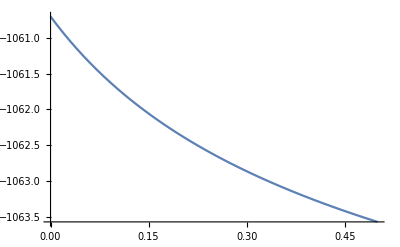

```mathematica
Plot[LOGpIposterior3[g10,g2,g40],g2range]
```

```mathematica
(*maximum at 0, g20 did not change*)
```

```mathematica
laH3g2=-D[LOGpIposterior3[g10,g2,g30],{g2,1}]/.g2->g20;
```

```mathematica
LOGpIposterior3[g10,g20,g40]//N
```

-1060.7

#### Final Accounting

```mathematica
laLOGm3=LOGpIposterior3[g10,g20,g40]+2/2 Log[2π]-1/2 Log[laH3g1]-1/2 Log[laH3g4]-Log[laH3g2]//N
```

-1067.33

```mathematica
B31=Exp[(laLOGm3-laLOGm1)]
```

127.987

```mathematica
lB31=(laLOGm3-laLOGm1)/Log[10]
```

2.10716

```mathematica
pointEstimator3=mean3/.{g1->g10,g2->g20,g4->g40}//N;
pointEstimator3⟦1⟧ (*intercept*)
pointEstimator3⟦3⟧ (*slope Stress*)
pointEstimator3⟦2⟧ (*slope Age*)
Variance[pointEstimator3⟦Range[4,m+3]⟧] (*variance of random intercept*)
Variance[pointEstimator3⟦Range[m+4,m+l+3]⟧] (*variance of random slope*)
(-2exponent3[g10,g20,g40]//N)/(n-2)(* variance of residual*)
```

1.80879

0.239166

-0.443439

0.123278

0.0240866

0.174758

## AGE, Random Intercept, STRESS, STRESSxAGE, Random Slope

### Model 4aS1

```mathematica
(*g1 from previous mode,  g2, g3 near 0, update g4*)g10//N
```

0.134362

```mathematica
cLOGlikelihood4=Expand[-1/2 Apply[Plus,(WellBeing-b0 -b1 Age -b2 Stress-b3 Age Stress- vW-vU)^2]-(n g1)/(2m)Apply[Plus,iW^2]-(s g2)/2 b2^2-(a g3)/2 b3^2-(n g4)/(2l)Apply[Plus,iU^2]]/.{g1->g10,g2->g20,g3->g30};
```

```mathematica
parameters4=Join[{b0,b1,b2,b3},iW,iU];zeros4=Join[{b0->0,b1->0,b2->0,b3->0},Table[Subscript[w, i]->0,{i,1,m}],Table[Subscript[u, i]->0,{i,1,l}]];
```

```mathematica
Hessian4=Simplify@Table[-D[cLOGlikelihood4,parameters4⟦i⟧,parameters4⟦j⟧],{i,1,4+m+l},{j,1,4+m+l}];
```

```mathematica
gradient4=Simplify@Table[-D[cLOGlikelihood4,parameters4⟦i⟧],{i,1,4+m+l}]/.zeros4;
```

```mathematica
detH4[g1_,g2_,g3_,g4_]=Simplify@Det[Hessian4];
```

```mathematica
LOGdetH4[g1_,g2_,g3_,g4_]=PowerExpand@Log@detH4[g1,g2,g3,g4];
```

```mathematica
mean4=-LinearSolve[Hessian4,gradient4];
```

```mathematica
exponent4[g1_,g2_,g3_,g4_]=Expand[-1/2 Apply[Plus,WellBeing^2]]-1/2 Apply[Plus,mean4 gradient4];
```

```mathematica
(*.10 LOGpIposterior4[g1_,g2_,g4_]=Log[(((n g1)/m)^(m/2)(s g2)^(1/2)(a g3)^(1/2)((n g4)/l)^(l/2)Gamma[(n-2)/2])/((2π)^((n-2)/2)detH4[g1,g2,g3,g4]^(1/2)(-exponent4[g1,g2,g3,g4])^((n-2)/2))Exp[-g1/2]/(√(2 π g1))Exp[-g2/2]/(√(2 π g2))Exp[-g3/2]/(√(2 π g3))Exp[-g4/2]/(√(2 π g4))];*)
```

```mathematica
LOGpIposterior4[g1_,g2_,g3_,g4_]=m/2 Log[(n g1)/m]+1/2 Log[s g2]+1/2 Log[a g3]+l/2 Log[(n g4)/l]+LogGamma[(n-2)/2]-(n-2)/2 Log[-exponent4[g1,g2,g3,g4]]-(n+2)/2 Log[2π]-1/2 Log[g1 g2 g3 g4]-1/2 LOGdetH4[g1,g2,g3,g4]-g1/2-g2/2-g3/2-g4/2;
```

### Laplace Approximation

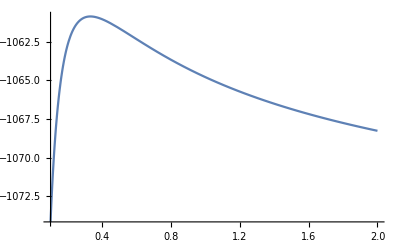

```mathematica
Plot[LOGpIposterior4[g10,g20,g30,g4],g4range]
```

```mathematica
max4a=NMaximize[{LOGpIposterior4[g10,g20,g30,g4],g4range⟦2⟧<g4<g4range⟦3⟧},g4]
```

{-1060.84,{g4→0.33171}}

```mathematica
g40=Round[max4a⟦2,1,2⟧ MyPrecision]/MyPrecision;
```

```mathematica
LOGpIposterior4[g10,g20,g30,g40]//N
```

-1060.84

### Model 4bS1

```mathematica
(*update g1*)
```

```mathematica
cLOGlikelihood4=Expand[-1/2 Apply[Plus,(WellBeing-b0 -b1 Age -b2 Stress-b3 Age Stress- vW-vU)^2]-(n g1)/(2m)Apply[Plus,iW^2]-(s g2)/2 b2^2-(a g3)/2 b3^2-(n g4)/(2l)Apply[Plus,iU^2]]/.{g2->g20,g3->g30,g4->g40};
```

```mathematica
Hessian4=Simplify@Table[-D[cLOGlikelihood4,parameters4⟦i⟧,parameters4⟦j⟧],{i,1,4+m+l},{j,1,4+m+l}];
```

```mathematica
gradient4=Simplify@Table[-D[cLOGlikelihood4,parameters4⟦i⟧],{i,1,4+m+l}]/.zeros4;
```

```mathematica
detH4[g1_,g2_,g3_,g4_]=Simplify@Det[Hessian4];
```

```mathematica
LOGdetH4[g1_,g2_,g3_,g4_]=PowerExpand@Log@detH4[g1,g2,g3,g4];
```

```mathematica
mean4=-LinearSolve[Hessian4,gradient4];
```

```mathematica
exponent4[g1_,g2_,g3_,g4_]=Expand[-1/2 Apply[Plus,WellBeing^2]]-1/2 Apply[Plus,mean4 gradient4];
```

```mathematica
(*.10 LOGpIposterior4[g1_,g2_,g4_]=Log[(((n g1)/m)^(m/2)(s g2)^(1/2)(a g3)^(1/2)((n g4)/l)^(l/2)Gamma[(n-2)/2])/((2π)^((n-2)/2)detH4[g1,g2,g3,g4]^(1/2)(-exponent4[g1,g2,g3,g4])^((n-2)/2))Exp[-g1/2]/(√(2 π g1))Exp[-g2/2]/(√(2 π g2))Exp[-g3/2]/(√(2 π g3))Exp[-g4/2]/(√(2 π g4))];*)
```

```mathematica
LOGpIposterior4[g1_,g2_,g3_,g4_]=m/2 Log[(n g1)/m]+1/2 Log[s g2]+1/2 Log[a g3]+l/2 Log[(n g4)/l]+LogGamma[(n-2)/2]-(n-2)/2 Log[-exponent4[g1,g2,g3,g4]]-(n+2)/2 Log[2π]-1/2 Log[g1 g2 g3 g4]-1/2 LOGdetH4[g1,g2,g3,g4]-g1/2-g2/2-g3/2-g4/2;
```

### Laplace Approximation

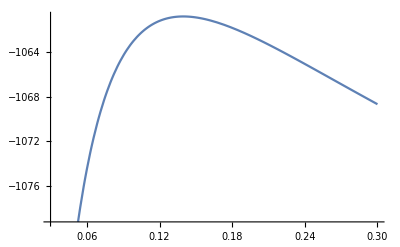

```mathematica
Plot[LOGpIposterior4[g1,g20,g30,g40],g1range]
```

```mathematica
max4b=NMaximize[{LOGpIposterior4[g1,g20,g30,g40],g1range⟦2⟧<g1<g1range⟦3⟧},g1](*very small change*)
```

{-1060.82,{g1→0.139598}}

```mathematica
g10=Round[max4b⟦2,1,2⟧ MyPrecision]/MyPrecision;
```

```mathematica
LOGpIposterior4[g10,g20,g30,g40]//N
```

-1060.82

### Model 4aS2

```mathematica
(*g1 from previous mode,  g2, g3 near 0, update g4*)g10//N
```

0.139598

```mathematica
cLOGlikelihood4=Expand[-1/2 Apply[Plus,(WellBeing-b0 -b1 Age -b2 Stress-b3 Age Stress- vW-vU)^2]-(n g1)/(2m)Apply[Plus,iW^2]-(s g2)/2 b2^2-(a g3)/2 b3^2-(n g4)/(2l)Apply[Plus,iU^2]]/.{g1->g10,g2->g20,g3->g30};
```

```mathematica
parameters4=Join[{b0,b1,b2,b3},iW,iU];zeros4=Join[{b0->0,b1->0,b2->0,b3->0},Table[Subscript[w, i]->0,{i,1,m}],Table[Subscript[u, i]->0,{i,1,l}]];
```

```mathematica
Hessian4=Simplify@Table[-D[cLOGlikelihood4,parameters4⟦i⟧,parameters4⟦j⟧],{i,1,4+m+l},{j,1,4+m+l}];
```

```mathematica
gradient4=Simplify@Table[-D[cLOGlikelihood4,parameters4⟦i⟧],{i,1,4+m+l}]/.zeros4;
```

```mathematica
detH4[g1_,g2_,g3_,g4_]=Simplify@Det[Hessian4];
```

```mathematica
LOGdetH4[g1_,g2_,g3_,g4_]=PowerExpand@Log@detH4[g1,g2,g3,g4];
```

```mathematica
mean4=-LinearSolve[Hessian4,gradient4];
```

```mathematica
exponent4[g1_,g2_,g3_,g4_]=Expand[-1/2 Apply[Plus,WellBeing^2]]-1/2 Apply[Plus,mean4 gradient4];
```

```mathematica
(*.10 LOGpIposterior4[g1_,g2_,g4_]=Log[(((n g1)/m)^(m/2)(s g2)^(1/2)(a g3)^(1/2)((n g4)/l)^(l/2)Gamma[(n-2)/2])/((2π)^((n-2)/2)detH4[g1,g2,g3,g4]^(1/2)(-exponent4[g1,g2,g3,g4])^((n-2)/2))Exp[-g1/2]/(√(2 π g1))Exp[-g2/2]/(√(2 π g2))Exp[-g3/2]/(√(2 π g3))Exp[-g4/2]/(√(2 π g4))];*)
```

```mathematica
LOGpIposterior4[g1_,g2_,g3_,g4_]=m/2 Log[(n g1)/m]+1/2 Log[s g2]+1/2 Log[a g3]+l/2 Log[(n g4)/l]+LogGamma[(n-2)/2]-(n-2)/2 Log[-exponent4[g1,g2,g3,g4]]-(n+2)/2 Log[2π]-1/2 Log[g1 g2 g3 g4]-1/2 LOGdetH4[g1,g2,g3,g4]-g1/2-g2/2-g3/2-g4/2;
```

### Laplace Approximation

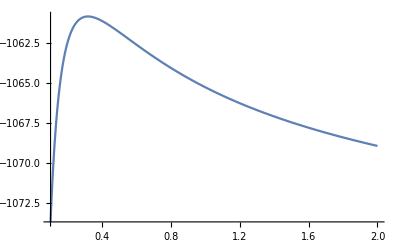

```mathematica
Plot[LOGpIposterior4[g10,g20,g30,g4],g4range]
```

```mathematica
max4a=NMaximize[{LOGpIposterior4[g10,g20,g30,g4],g4range⟦2⟧<g4<g4range⟦3⟧},g4]
```

{-1060.81,{g4→0.317625}}

```mathematica
g40=Round[max4a⟦2,1,2⟧ MyPrecision]/MyPrecision;
```

```mathematica
laH4g4=-D[LOGpIposterior4[g10,g20,g40,g4],{g4,2}]/.g4->g40;
```

```mathematica
LOGpIposterior4[g10,g20,g30,g40]//N
```

-1060.81

### Model 4bS2

```mathematica
(*g4 from previous, update g1*)g40//N
```

0.317625

```mathematica
cLOGlikelihood4=Expand[-1/2 Apply[Plus,(WellBeing-b0 -b1 Age -b2 Stress-b3 Age Stress- vW-vU)^2]-(n g1)/(2m)Apply[Plus,iW^2]-(s g2)/2 b2^2-(a g3)/2 b3^2-(n g4)/(2l)Apply[Plus,iU^2]]/.{g2->g20,g3->g30,g4->g40};
```

```mathematica
Hessian4=Simplify@Table[-D[cLOGlikelihood4,parameters4⟦i⟧,parameters4⟦j⟧],{i,1,4+m+l},{j,1,4+m+l}];
```

```mathematica
gradient4=Simplify@Table[-D[cLOGlikelihood4,parameters4⟦i⟧],{i,1,4+m+l}]/.zeros4;
```

```mathematica
detH4[g1_,g2_,g3_,g4_]=Simplify@Det[Hessian4];
```

```mathematica
LOGdetH4[g1_,g2_,g3_,g4_]=PowerExpand@Log@detH4[g1,g2,g3,g4];
```

```mathematica
mean4=-LinearSolve[Hessian4,gradient4];
```

```mathematica
exponent4[g1_,g2_,g3_,g4_]=Expand[-1/2 Apply[Plus,WellBeing^2]]-1/2 Apply[Plus,mean4 gradient4];
```

```mathematica
(*.10 LOGpIposterior4[g1_,g2_,g4_]=Log[(((n g1)/m)^(m/2)(s g2)^(1/2)(a g3)^(1/2)((n g4)/l)^(l/2)Gamma[(n-2)/2])/((2π)^((n-2)/2)detH4[g1,g2,g3,g4]^(1/2)(-exponent4[g1,g2,g3,g4])^((n-2)/2))Exp[-g1/2]/(√(2 π g1))Exp[-g2/2]/(√(2 π g2))Exp[-g3/2]/(√(2 π g3))Exp[-g4/2]/(√(2 π g4))];*)
```

```mathematica
LOGpIposterior4[g1_,g2_,g3_,g4_]=m/2 Log[(n g1)/m]+1/2 Log[s g2]+1/2 Log[a g3]+l/2 Log[(n g4)/l]+LogGamma[(n-2)/2]-(n-2)/2 Log[-exponent4[g1,g2,g3,g4]]-(n+2)/2 Log[2π]-1/2 Log[g1 g2 g3 g4]-1/2 LOGdetH4[g1,g2,g3,g4]-g1/2-g2/2-g3/2-g4/2;
```

### Laplace Approximation

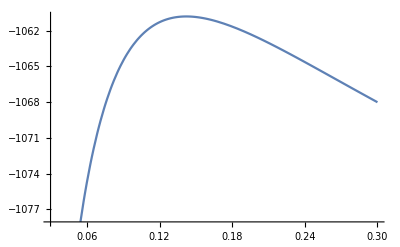

```mathematica
Plot[LOGpIposterior4[g1,g20,g30,g40],g1range]
```

```mathematica
max4b=NMaximize[{LOGpIposterior4[g1,g20,g30,g40],g1range⟦2⟧<g1<g1range⟦3⟧},g1](*very small change*)
```

{-1060.8,{g1→0.142136}}

```mathematica
g10=Round[max4b⟦2,1,2⟧ MyPrecision]/MyPrecision;
```

```mathematica
laH4g1=-D[LOGpIposterior4[g1,g20,g30,g40],{g1,2}]/.g1->g10;
```

```mathematica
LOGpIposterior4[g10,g20,g30,g40]//N
```

-1060.8

### Model 4c

```mathematica
(*update g3*)
```

```mathematica
cLOGlikelihood4=Expand[-1/2 Apply[Plus,(WellBeing-b0 -b1 Age -b2 Stress-b3 Age Stress- vW-vU)^2]-(n g1)/(2m)Apply[Plus,iW^2]-(s g2)/2 b2^2-(a g3)/2 b3^2-(n g4)/(2l)Apply[Plus,iU^2]]/.{g1->g10,g2->g20,g4->g40};
```

```mathematica
Hessian4=Simplify@Table[-D[cLOGlikelihood4,parameters4⟦i⟧,parameters4⟦j⟧],{i,1,4+m+l},{j,1,4+m+l}];
```

```mathematica
gradient4=Simplify@Table[-D[cLOGlikelihood4,parameters4⟦i⟧],{i,1,4+m+l}]/.zeros4;
```

```mathematica
detH4[g1_,g2_,g3_,g4_]=Simplify@Det[Hessian4];
```

```mathematica
LOGdetH4[g1_,g2_,g3_,g4_]=PowerExpand@Log@detH4[g1,g2,g3,g4];
```

```mathematica
mean4=-LinearSolve[Hessian4,gradient4];
```

```mathematica
exponent4[g1_,g2_,g3_,g4_]=Expand[-1/2 Apply[Plus,WellBeing^2]]-1/2 Apply[Plus,mean4 gradient4];
```

```mathematica
(*.10 LOGpIposterior4[g1_,g2_,g4_]=Log[(((n g1)/m)^(m/2)(s g2)^(1/2)(a g3)^(1/2)((n g4)/l)^(l/2)Gamma[(n-2)/2])/((2π)^((n-2)/2)detH4[g1,g2,g3,g4]^(1/2)(-exponent4[g1,g2,g3,g4])^((n-2)/2))Exp[-g1/2]/(√(2 π g1))Exp[-g2/2]/(√(2 π g2))Exp[-g3/2]/(√(2 π g3))Exp[-g4/2]/(√(2 π g4))];*)
```

```mathematica
LOGpIposterior4[g1_,g2_,g3_,g4_]=m/2 Log[(n g1)/m]+1/2 Log[s g2]+1/2 Log[a g3]+l/2 Log[(n g4)/l]+LogGamma[(n-2)/2]-(n-2)/2 Log[-exponent4[g1,g2,g3,g4]]-(n+2)/2 Log[2π]-1/2 Log[g1 g2 g3 g4]-1/2 LOGdetH4[g1,g2,g3,g4]-g1/2-g2/2-g3/2-g4/2;
```

### Laplace Approximation

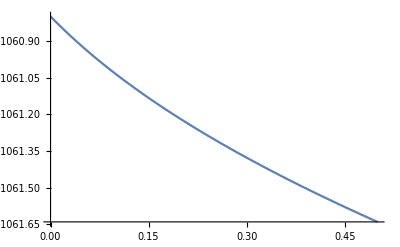

```mathematica
Plot[LOGpIposterior4[g10,g20,g3,g40],g3range]
```

```mathematica
(*nearly 0 - need an exponential approximation, g3 unchenched*)
```

```mathematica
laH4g3=-D[LOGpIposterior4[g10,g20,g3,g40],{g3,1}]/.g3->g30;(*g30 did not change*)
```

```mathematica
LOGpIposterior4[g10,g20,g30,g40]//N
```

-1060.8

### Model 4d

```mathematica
(*update g2*)
```

```mathematica
cLOGlikelihood4=Expand[-1/2 Apply[Plus,(WellBeing-b0 -b1 Age -b2 Stress-b3 Age Stress- vW-vU)^2]-(n g1)/(2m)Apply[Plus,iW^2]-(s g2)/2 b2^2-(a g3)/2 b3^2-(n g4)/(2l)Apply[Plus,iU^2]]/.{g1->g10,g3->g30,g4->g40};
```

```mathematica
Hessian4=Simplify@Table[-D[cLOGlikelihood4,parameters4⟦i⟧,parameters4⟦j⟧],{i,1,4+m+l},{j,1,4+m+l}];
```

```mathematica
gradient4=Simplify@Table[-D[cLOGlikelihood4,parameters4⟦i⟧],{i,1,4+m+l}]/.zeros4;
```

```mathematica
detH4[g1_,g2_,g3_,g4_]=Simplify@Det[Hessian4];
```

```mathematica
LOGdetH4[g1_,g2_,g3_,g4_]=PowerExpand@Log@detH4[g1,g2,g3,g4];
```

```mathematica
mean4=-LinearSolve[Hessian4,gradient4];
```

```mathematica
exponent4[g1_,g2_,g3_,g4_]=Expand[-1/2 Apply[Plus,WellBeing^2]]-1/2 Apply[Plus,mean4 gradient4];
```

```mathematica
(*.10 LOGpIposterior4[g1_,g2_,g4_]=Log[(((n g1)/m)^(m/2)(s g2)^(1/2)(a g3)^(1/2)((n g4)/l)^(l/2)Gamma[(n-2)/2])/((2π)^((n-2)/2)detH4[g1,g2,g3,g4]^(1/2)(-exponent4[g1,g2,g3,g4])^((n-2)/2))Exp[-g1/2]/(√(2 π g1))Exp[-g2/2]/(√(2 π g2))Exp[-g3/2]/(√(2 π g3))Exp[-g4/2]/(√(2 π g4))];*)
```

```mathematica
LOGpIposterior4[g1_,g2_,g3_,g4_]=m/2 Log[(n g1)/m]+1/2 Log[s g2]+1/2 Log[a g3]+l/2 Log[(n g4)/l]+LogGamma[(n-2)/2]-(n-2)/2 Log[-exponent4[g1,g2,g3,g4]]-(n+2)/2 Log[2π]-1/2 Log[g1 g2 g3 g4]-1/2 LOGdetH4[g1,g2,g3,g4]-g1/2-g2/2-g3/2-g4/2;
```

### Laplace Approximation

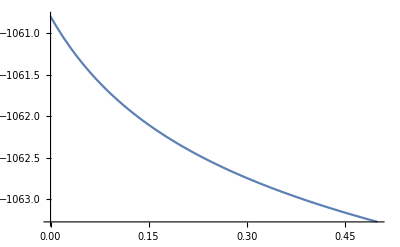

```mathematica
Plot[LOGpIposterior4[g10,g2,g30,g40],g2range]
```

```mathematica
(*nearly 0 - need an exponential approximation g2 unchanged*)
```

```mathematica
laH4g2=-D[LOGpIposterior4[g10,g2,g30,g40],{g2,1}]/.g2->g20;(*g20 did not change*)
```

```mathematica
LOGpIposterior4[g10,g20,g30,g40]//N
```

-1060.8

#### Final Accounting

```mathematica
laLOGm4=LOGpIposterior4[g10,g20,g30,g40]+2/2 Log[2π]-1/2 Log[laH4g1]-1/2 Log[laH4g4]-Log[laH4g2]-Log[laH4g3]//N
```

-1068.69

```mathematica
B41=Exp[(laLOGm4-laLOGm1)]
```

32.8792

```mathematica
lB41=(laLOGm4-laLOGm1)/Log[10.]
```

1.51692

```mathematica
pointEstimator4=mean4/.{g1->g10,g2->g20,g3->g30,g4->g40}//N;
pointEstimator4⟦1⟧ (*intercept*)
pointEstimator4⟦3⟧ (*slope Stress*)
pointEstimator4⟦2⟧ (*slope Age*)
pointEstimator4⟦4⟧ (*slope Age x Stress*)
Variance[pointEstimator4⟦Range[5,m+4]⟧] (*variance of random intercept*)
Variance[pointEstimator4⟦Range[m+5,m+l+4]⟧] (*variance of random slope*)
(-2exponent4[g10,g20,g30,g40]//N)/(n-2)(* variance of residual*)
```

1.80863

0.244722

-0.443141

-0.00607065

0.109217

0.0308497

0.174276

## Various Bayes Factors

```mathematica
allBFac={laLOGm0,laLOGm1,laLOGm2,laLOGm3,laLOGm4}//N
```

{-1074.15,-1072.18,-1074.72,-1067.33,-1068.69}

```mathematica
Table[Exp[allBFac⟦i⟧-allBFac⟦j⟧],{i,1,5},{j,1,5}]//MatrixForm
```

(1. | 0.139277 | 1.76682 | 0.00108821 | 0.00423601
7.17996 | 1. | 12.6857 | 0.00781331 | 0.0304144
0.565989 | 0.0788289 | 1. | 0.000615915 | 0.00239753
918.939 | 127.987 | 1623.6 | 1. | 3.89263
236.071 | 32.8792 | 417.096 | 0.256895 | 1.)